# Polar Coordinates

### Author

Eric W. Weisstein
March 9, 2014

This notebook downloaded from http://mathworld.wolfram.com/notebooks/CoordinateGeometry/PolarCoordinates.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PolarCoordinates.html.

©2014 Wolfram Research, Inc. except for portions noted otherwise

### Initialization

```mathematica
hat[v_]:=OverHat[StyleForm[v,FontWeight->"Bold",FontSlant->"Plain"]];
```

```mathematica
TraditionalDisplay[g_]:=(g/.{Derivative[1][x_]:>Overscript[x,"."],
Derivative[2][x_]:>Overscript[x,".."]}/.f_[t]:>f)//TraditionalForm
```

## Figures

### Axes

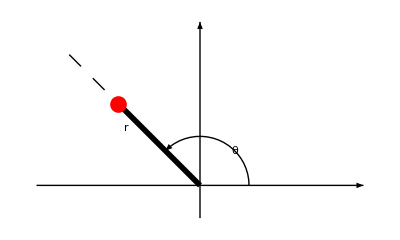

```mathematica
Graphics[{
{Arrow[{{-1,0},{1,0}}],Arrow[{{0,-.2},{0,1}}]},
{Thickness[.01],Arrow[{{0,0},{-.5,.5}}]},{Dashing[.03],Line[{.8{-1,1},{-.5,.5}}]},
{Red,PointSize[.03],Point[{-.5,.5}]},
Arrow[.3Table[Through[{Cos,Sin}[3π/4  k/20]],{k,0,20}]],
Text[Style[Row[{" ","θ"," "}]],.21{1,1},Background->White],
Text[Style["r",Italic],{-.45,.35},Background->White]
}]
```

### Rings

```mathematica
PolarPlot[0,{q,0,2π},PolarAxes->True]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

-Graphics-

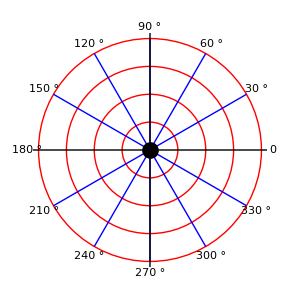

```mathematica
Graphics[{
{Red,Table[Circle[{0,0},r],{r,1/4,1,1/4}]},
{Blue,Line[{-#,#}&/@Table[Through[{Cos,Sin}[π k/6]],{k,5}]]},
Thick,Line[1.05{{{-1,0},{1,0}},{{0,-1},{0,1}}}],
Table[Text[d Degree,1.1Through[{Cos,Sin}[d Degree]],Background->White],{d,0,330,30}],
PointSize[.04],Point[{0,0}]
},ImageSize->300]
```

## Cartesian Basis

```mathematica
r[x_,y_]:=Sqrt[x[t]^2+y[t]^2]hat[r][t]
```

```mathematica
r[x,y]
```

√(x[t]^2+y[t]^2) r̂[t]

### r̂

```mathematica
hat/@{x,y}.{x[t],y[t]}/Sqrt[Dot[{x[t],y[t]},{x[t],y[t]}]]//TraditionalDisplay
```

(x x̂+y ŷ)/(√(x^2+y^2))

### ṙ

```mathematica
r
```

r

```mathematica
Together/@Collect[Expand[D[r[x,y],t]], hat[r][t]]//TraditionalDisplay
```

(r̂ (x ẋ+y ẏ))/(√(x^2+y^2))+√(x^2+y^2) OverDot[r̂]

### OverDot[r̂]

```mathematica
Simplify[D[OverHat[StyleForm[#,FontWeight->"Bold",FontSlant->"Plain"]]&/@{x,y}.{x[t],y[t]}/Sqrt[Dot[{x[t],y[t]},{x[t],y[t]}]],t]]//TraditionalDisplay
```

((x ŷ-y x̂) (x ẏ-y ẋ))/((x^2+y^2)^(3/2))

## Polar Coordinates

```mathematica
rvec=r[t]{Cos[θ[t]],Sin[θ[t]]};
```

### r̂

```mathematica
rhat=Simplify[#/Sqrt[#.#]&@D[rvec,r[t]]]
```

{Cos[θ[t]],Sin[θ[t]]}

### θ̂

```mathematica
that=PowerExpand[Simplify[#/Sqrt[#.#]&@D[rvec,θ[t]]]]
```

General::spell1: Possible spelling error: new symbol name "that" is similar to existing symbol "rhat".

{-Sin[θ[t]],Cos[θ[t]]}

### ṙ

```mathematica
dr=D[rvec,t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
Simplify[hat[r] dr.rhat+hat[θ]dr.that]//TraditionalDisplay
```

r̂ ṙ+r θ̂ θ̇

### r^(..)

```mathematica
dr2=D[rvec,{t,2}]
```

{-2 Sin[θ[t]] r'[t] θ'[t]+Cos[θ[t]] r''[t]+r[t] (-Cos[θ[t]] θ'[t]^2-Sin[θ[t]] θ''[t]),2 Cos[θ[t]] r'[t] θ'[t]+Sin[θ[t]] r''[t]+r[t] (-Sin[θ[t]] θ'[t]^2+Cos[θ[t]] θ''[t])}

```mathematica
Simplify[hat[r] dr2.rhat+hat[θ]dr2.that]//TraditionalDisplay
```

r̂ (r^(..)-r (θ̇)^2)+θ̂ (2 ṙ θ̇+r θ^(..))

### OverDot[r̂]

```mathematica
Simplify[(hat[r]#.rhat+hat[θ]#.that)&[D[rhat,t]]]//TraditionalDisplay
```

θ̂ θ̇

### OverDot[θ̂]

```mathematica
Simplify[(hat[r]#.rhat+hat[θ]#.that)&[D[that,t]]]//TraditionalDisplay
```

-r̂ θ̇